# Sub projects for Bulge Chase

Implement the Bulge to Spike transformation in Julia.  You need the Julia co

The Julia Schur decomposition is described at https://docs.julialang.org/en/v1/stdlib/LinearAlgebra/#LinearAlgebra.schur

First work out how to call the command and get the bits you need.

Work out how to embed the Q in a big matrix to spike a bulge of size b at the bottom of a large square matrix of size n

Work out how to embed the Q in a big matrix to spike a bulge of size b at the top of a large square matrix of size n.

Work out how to spike a bulge of size b near the middle of a large square matrix of size n.

Work out how to spike two bulges of size b near the middle of a large square matrix of size n.

It is fine to make synthetic test problems by just adding blocks to a Hessenberg reduced matrix.

Describe the spikes that result.

Extension try to work out how to sort the spike entries from large to small by absolute value! Of course you need to preserve eigenvalues.

Implement a newton method in Julia

Build a function that takes values from functions f:ℝ^n->ℝ^n and df:ℝ^n->ℝ^(n×n) with a current guess x and returns the updated x-LinearSolve[df,x].

Check and see if your code works for values from f:ℝ^n->ℝ^m and df:ℝ^n->ℝ^(m×n).  If it does not learn how to implement the minimum change solution in Julia.  If it does find documentation that it gives the min change solution.

Test your function in a script on the function plotted below.  Just define the f and df functions in Julia. I converted the df output to pretty form so that it is easier to read and/or copy and paste! You should be able to compute the single zero visible in the window.

((cos(x1+x2)+4) cos(sin(x1+x2)+4 x1) | cos(x1+x2) cos(sin(x1+x2)+4 x1)
-4 sin(4 x1-sin(x2)) | cos(x2) sin(4 x1-sin(x2)))

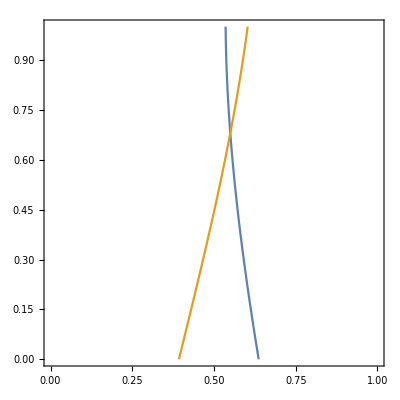

```mathematica
f[{x1_,x2_}]:= {Sin[4x1 + Sin[x1 +x2]],Cos[4 x1-Sin[x2]]}
df[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2}}]
ContourPlot[ {
f[{x1,x2}][[1]]==0,
f[{x1,x2}][[2]]==0
},{x1,0,1},{x2,0,1}]
```

Test your function in a script on the function below. Check it converges to a solution!

```mathematica
f[{x1_,x2_,x3_}]:= {x1 + x2+x3,Sin[x1 x2]+x3 }
 df[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3}}]
```

(1 | 1 | 1
x2 cos(x1 x2) | x1 cos(x1 x2) | 1)

Learn how to make a function that takes a function as argument in Julia.

Make a function that takes the functions f and df and runs Newton’s method from an initial guess until convergence.

Learn how to use an AD tool in Julia

Look on JuliaDiff for a list of AD tools.  Find one you think is well documented.  I have been using ForwardDiff.

Read the documentation.

Understand the examples.

Define the Rosenbrock function f:ℝ^n→ℝ^n from the wiki page https://en.wikipedia.org/wiki/Rosenbrock_function use the “second more involved variant”.

Use your AD tool to compute (∂f)/(∂x_1) in dimension 20 evaluated at the vector of all 1s.  Confirm that your derivative is correct in some way.  Hint plot your computed derivative against a finite difference approximation as a function of h.

Use your AD tool to compute (∂f)/(∂x_5) in dimension 22 evaluated at the vector of all 1s.  Confirm that your derivative is correct in some way.  Hint plot your computed derivative against a finite difference approximation as a function of h.

Use your AD tool to compute the directional derivative (∂f)/(∂u) where u_i=sin(i/11) in dimension 22 evaluated at the vector of all 1s.  Confirm that your derivative is correct in some way.